# Archetypal Quest

### Let’s start easy: Mean

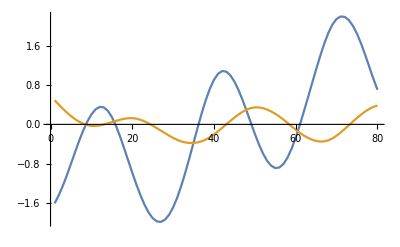

```mathematica
archetypalMeanYes=Table[Mean[Table[reducedOxyYes80[[x,y]],{x,30}]],{y,2}];
ListLinePlot[archetypalMeanYes]
```

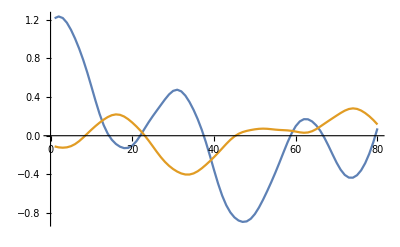

```mathematica
archetypalMeanNo = Table[Mean[Table[reducedOxyNo80[[x,y]],{x,30}]],{y,2}];
ListLinePlot[archetypalMeanNo]
```

### Time to generalize to various metrics

```mathematica
archetypal[f_]:=ListLinePlot[{Legended[f[Table[reducedOxyYes80[[x,1]],{x,30}]],"Oxy Yes"],Legended[f[Table[reducedOxyNo80[[x,1]],{x,30}]],"Oxy No"]},PlotLabel->f]
```

Test on the Mean function:

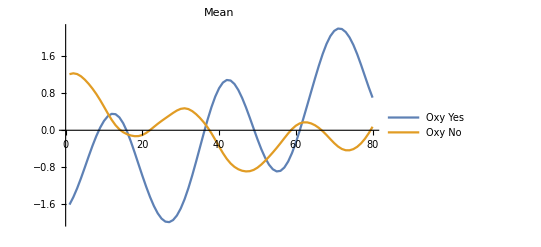

```mathematica
archetypal[Mean]
```

Generation of a list of archetypal based on standard statistical measures:

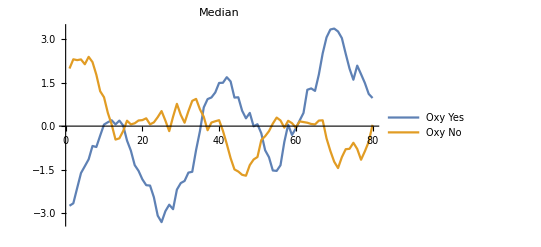
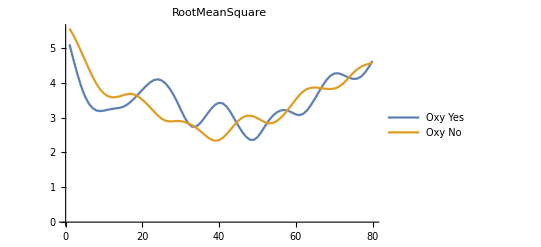
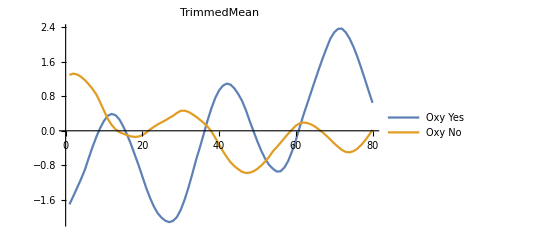
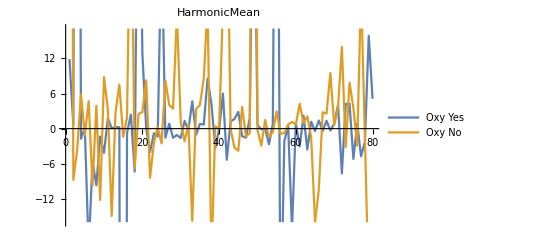
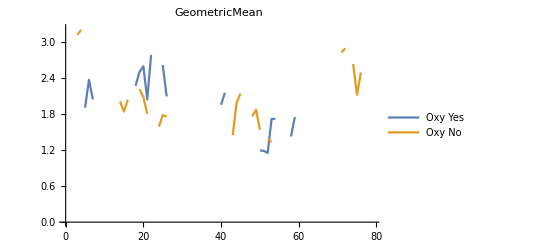
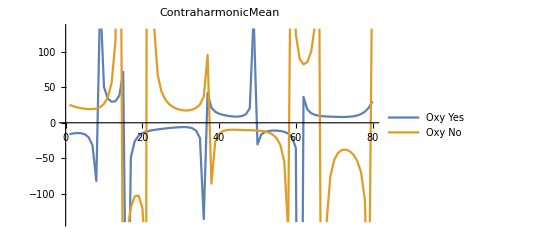
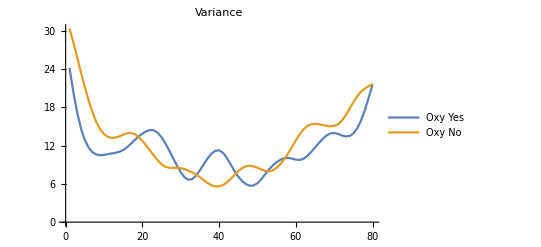
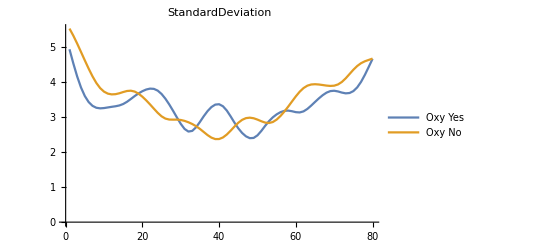
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
energy=Total@(#^2)&;
stats={Mean,Median,RootMeanSquare,TrimmedMean,HarmonicMean,GeometricMean,ContraharmonicMean,Variance,StandardDeviation,MeanDeviation,MedianDeviation,QuartileDeviation,InterquartileRange,Skewness,Kurtosis,QuartileSkewness,Entropy,energy};
Column[Style[archetypal[#],Larger]&/@stats]
```

#### Comment about the above results :

It seems like only the Mean function can give two quite different archetypals

## Experiments with DTW

```mathematica
WarpingDistance[reducedOxyYes80[[1,1]],archetypalMeanYes]
```

140.75

```mathematica
wrp[signal_List,arch_List] :=WarpingDistance[signal,arch]
```

```mathematica
distYesYes = Table[wrp[reducedOxyYes80[[x,1]],archetypalMeanYes[[1]]],{x,30}];
distYesNo = Table[wrp[reducedOxyYes80[[x,1]],archetypalMeanNo[[1]]],{x,30}];
distNoYes = Table[wrp[reducedOxyNo80[[x,1]],archetypalMeanYes[[1]]],{x,30}];
distNoNo = Table[wrp[reducedOxyNo80[[x,1]],archetypalMeanNo[[1]]],{x,30}];
```

```mathematica
ListPlot[{Legended[distNoNo,"Distances of No from No"],Legended[distNoYes,"Distances of No from Yes"]}]
Histogram[{Legended[distYesYes,"Distances of Yes from Yes"],Legended[distNoYes,"Distances of No from Yes"]}]
Histogram[{Legended[distNoNo,"Distances of No from No"],Legended[distYesYes,"Distances of Yes from Yes"]}]
```

### ScatterPlot

{dYes, dNo} per ogni vec

```mathematica
distYesYesYesNo = Table[{wrp[reducedOxyYes80[[x,1]],archetypalMeanYes[[1]]],wrp[reducedOxyYes80[[x,1]],archetypalMeanNo[[1]]]},{x,30}];
```

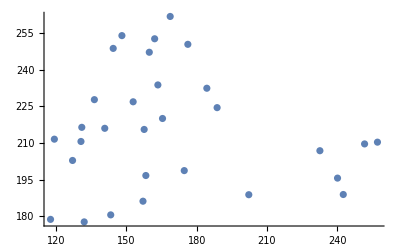

```mathematica
ListPlot[distYesYesYesNo]
```

```mathematica
distNoNoNoYes = Table[{wrp[reducedOxyNo80[[x,1]],archetypalMeanNo[[1]]],wrp[reducedOxyNo80[[x,1]],archetypalMeanYes[[1]]]},{x,30}];
```

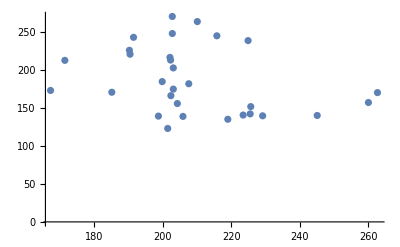

```mathematica
ListPlot[distNoNoNoYes]
```

```mathematica
30*0.3
```

9.